# Some minimal bimolecular mass-action systems with limit cycles

Balázs Boros and Josef Hofbauer

Department of Mathematics, University of Vienna, Austria

This Mathematica Notebook is a supplementary material to the paper which has the same title as this document.
It contains some of the calculations appearing in the paper.

## 0 The first and the second focal values

Below we collect some functions that will be used later on for computing the first and the second focal values. It is based on the Scholarpedia articles
http://www.scholarpedia.org/article/Andronov-Hopf_bifurcation (by Y. A. Kuznetsov) and
http://www.scholarpedia.org/article/Bautin_bifurcation (by J. Guckenheimer and Y. A. Kuznetsov).

```mathematica
Idx[set_,n_]:=Module[{seq},seq=(Table[Count[set,i],{i,n}]/.List->Sequence);seq];

GetDerivatives[f_,equilibrium_]:=Module[{derivatives,order,deriv,i,j,k,A,B,CC,DD,EE},
n=Length[f];
A=D[f,{{x,y,z}}]/.equilibrium;
derivatives={};
order=2;
For[i=0,i≤order,i++,For[j=0,j≤order-i,j++,For[k=0,k≤order-i-j,k++,
deriv=Simplify[D[f,{x,i},{y,j},{z,k}]/.equilibrium];
derivatives=Join[derivatives,Simplify[{Subscript[F, i,j,k]->deriv[[1]],Subscript[G, i,j,k]->deriv[[2]],Subscript[H, i,j,k]->deriv[[3]]}]];
]]];
B[x_,y_]:=Sum[{Subscript[F, Idx[{k,l},n]],Subscript[G, Idx[{k,l},n]],Subscript[H, Idx[{k,l},n]]}x[[k]]y[[l]]/.derivatives,{k,n},{l,n}];
(*CC[x_,y_,z_]:=Sum[{Subscript[F, Idx[{k,l,m},n]],Subscript[G, Idx[{k,l,m},n]],Subscript[H, Idx[{k,l,m},n]]}x[[k]]y[[l]]z[[m]]/.derivatives,{k,n},{l,n},{m,n}];*)
(* because of the bimolecularity, all derivatives of order 3 and higher vanish *)
CC[x_,y_,z_]:={0,0,0};
DD[x_,y_,z_,s_]:={0,0,0};
EE[x_,y_,z_,s_,t_]:={0,0,0};
(* the reason for the double symbols CC, DD, EE is that C, D, E are protected in Mathematica *)
{A,B,CC,DD,EE}
];

GetHopf[A_]:=Module[{a,charpol,A2A1minusA0},
charpol=Collect[-CharacteristicPolynomial[A,λ],λ];
{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}=Simplify[CoefficientList[charpol,λ]];
A2A1minusA0=Simplify[Subscript[a, 1] Subscript[a, 2]-Subscript[a, 0]];
{charpol,Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],A2A1minusA0}
];

GetEigvectors[A_,om_]:=Module[{n,mtx,pconj,q,qconj,normalize},
n=Length[A];
mtx=A-om ⅈ IdentityMatrix[n];
q=NullSpace[mtx[[Range[1,n-1]]]][[1]];
(* Notice that q is not normalised. The normalisation has relevance only when the second focal value is computed for parameter values, where the first focal value does not vanish. *)
mtx=Aᵀ-om ⅈ IdentityMatrix[n];
pconj=NullSpace[mtx[[Range[1,n-1]]]][[1]];
normalize=FullSimplify[pconj.q];
pconj=pconj/normalize;
qconj=FullSimplify[ComplexExpand[q*]];
{pconj,q,qconj}
];

GetL1[A_,B_,CC_]:=Module[{n,pconj,q,qconj,v1,v2,v3,c1,numer,denom,a,b,c,d,L1κω},
n=Length[A];
{pconj,q,qconj}=GetEigvectors[A,ω];
v1=CC[q,q,qconj];
v2=Simplify[B[q,Inverse[-A].B[q,qconj]]];
v3=Simplify[B[qconj,Inverse[2I ω IdentityMatrix[n]-A].B[q,q]]];
c1=Simplify[pconj.(1/2 v1+v2+1/2 v3)];
(* We take the real part in a bit complicated way: Re (a+bⅈ)/(c+dⅈ)=(ac+bd)/(c^2+d^2).
It seems to be faster than the standard solution would be. *)
numer=Numerator[c1];
denom=Denominator[c1];
a=Simplify[ComplexExpand[Re[numer]]];
b=Simplify[ComplexExpand[Im[numer]]];
c=Simplify[ComplexExpand[Re[denom]]];
d=Simplify[ComplexExpand[Im[denom]]];
L1κω=Simplify[(a c+b d)/(c^2+d^2)];
L1κω
];

GetL2[A_,B_,CC_,DD_,EE_]:=Module[{n,Id,omega,invA,inv2,inv3,pconj,q,qconj,h,prec,c,invbig},
n=Length[A];
Id=IdentityMatrix[n];
omega=√(Det[A]/Tr[A]);
invA=Inverse[A];
inv2=Simplify[Inverse[2 omega I Id-A]];
inv3=Simplify[Inverse[3 omega I Id-A]];
{pconj,q,qconj}=GetEigvectors[A,omega];
q=FullSimplify[q/. {ω->omega}];
pconj=FullSimplify[pconj/. {ω->omega}];
Subscript[h, 2,0]=FullSimplify[inv2.B[q,q]];
Subscript[h, 1,1]=FullSimplify[-invA.B[q,q*]];
prec=FullSimplify[CC[q,q,q*]+2 B[q,Subscript[h, 1,1]]+B[q*,Subscript[h, 2,0]]];
Subscript[c, 1]=FullSimplify[1/2 (pconj.prec)];
invbig=FullSimplify[Inverse[Join[Join[omega I Id-A,{q}ᵀ,2],{Join[pconj,{0}]}]]];
Subscript[h, 2,1]=FullSimplify[invbig.Join[FullSimplify[prec-2 Subscript[c, 1] q],{0}]][[1;;n]];
Subscript[h, 3,0]=FullSimplify[inv3.(CC[q,q,q]+3 B[q,Subscript[h, 2,0]])];
Subscript[h, 3,1]=FullSimplify[inv2.(DD[q,q,q,q*]+3 CC[q,q,Subscript[h, 1,1]]+3 CC[q,q*,Subscript[h, 2,0]]+3 B[Subscript[h, 2,0],Subscript[h, 1,1]]+B[q*,Subscript[h, 3,0]]+3 B[q,Subscript[h, 2,1]]-6 Subscript[c, 1] Subscript[h, 2,0])];
Subscript[h, 2,2]=FullSimplify[-invA.(DD[q,q,q*,q*]+4 CC[q,q*,Subscript[h, 1,1]]+CC[q*,q*,Subscript[h, 2,0]]+CC[q,q,Subscript[h, 2,0]*]+2 B[Subscript[h, 1,1],Subscript[h, 1,1]]+2 B[q,Subscript[h, 2,1]*]+2 B[q*,Subscript[h, 2,1]]+B[Subscript[h, 2,0]*,Subscript[h, 2,0]])];
Subscript[c, 2]=FullSimplify[1/12 (pconj.(EE[q,q,q,q*,q*]+DD[q,q,q,Subscript[h, 2,0]*]+3 DD[q,q*,q*,Subscript[h, 2,0]]+6 DD[q,q,q*,Subscript[h, 1,1]]+CC[q*,q*,Subscript[h, 3,0]]+3 CC[q,q,Subscript[h, 2,1]*]+6 CC[q,q*,Subscript[h, 2,1]]+3 CC[q,Subscript[h, 2,0]*,Subscript[h, 2,0]]+6 CC[q,Subscript[h, 1,1],Subscript[h, 1,1]]+6 CC[q*,Subscript[h, 2,0],Subscript[h, 1,1]]+2 B[q*,Subscript[h, 3,1]]+3 B[q,Subscript[h, 2,2]]+B[Subscript[h, 2,0]*,Subscript[h, 3,0]]+3 B[Subscript[h, 2,1]*,Subscript[h, 2,0]]+6 B[Subscript[h, 1,1],Subscript[h, 2,1]]))];
ComplexExpand[Re[Subscript[c, 2]]]
];
```

## 3 Feinberg-Berner oscillator

### Theorem 10

```mathematica
f=Subscript[κ, 1] x y{-1,-1,1}+Subscript[κ, 2] z{1,1,-1}+Subscript[κ, 3] z{1,0,-1}+Subscript[κ, 4] x{-1,0,1}+Subscript[κ, 5] x{1,0,0}+Subscript[κ, 6] x^2{-1,0,0}+Subscript[κ, 7] z{0,1,-1}+Subscript[κ, 8] y{0,-1,1};
```

#### (ii) The system is competitive.

After performing the  coordinate transformation, all the off-diagonal entries are negative everywhere on.

```mathematica
Print[MatrixForm[D[(f/.{z->-w}){1,1,-1},{{x,y,w}}]]];
```

(-y κ_1-κ_4+κ_5-2 x κ_6 | -x κ_1 | -κ_2-κ_3
-y κ_1 | -x κ_1-κ_8 | -κ_2-κ_7
-y κ_1-κ_4 | -x κ_1-κ_8 | -κ_2-κ_3-κ_7)

#### (iv) The unique positive equilibrium is .

```mathematica
equilibrium={x->1,y->1,z->1};
κsubst=Solve[(f/.equilibrium)==0,{Subscript[κ, 3],Subscript[κ, 5],Subscript[κ, 7]}][[1]];
Print[κsubst];
```

{κ_3→κ_4,κ_5→κ_1-κ_2+κ_6,κ_7→κ_1-κ_2+κ_8}

#### (v) Linear stability for .

```mathematica
g=f/.κsubst;
J=D[g,{{x,y,z}}]/.equilibrium;
{charpol,Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],A2A1minusA0}=GetHopf[J];
Print["Jacobian matrix: ",MatrixForm[J]];
Print["coefficients of the characteristic polynomial :"];
Print["    ",Subscript[a, 2]];
Print["    ",Subscript[a, 1]];
Print["    ",Subscript[a, 0]];
linstable=Reduce[Expand[A2A1minusA0]>0&&Subscript[κ, 1]<=Subscript[κ, 2]+2 Subscript[κ, 4]&&Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 4]>0&&Subscript[κ, 6]>0&&Subscript[κ, 8]>0&&Subscript[κ, 1]==1,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 6],Subscript[κ, 8],Subscript[κ, 1]}];
(* setting Subscript[κ, 1]=1 does not restrict generality, but reduces the number of unknowns and thus helps Reduce *)
Print["all eigenvalues have negative real part: ",linstable];
```

Jacobian matrix: (-κ_2-κ_4-κ_6 | -κ_1 | κ_2+κ_4
-κ_1 | -κ_1-κ_8 | κ_1+κ_8
κ_1+κ_4 | κ_1+κ_8 | -κ_1-κ_4-κ_8)

coefficients of the characteristic polynomial :

2 κ_1+κ_2+2 κ_4+κ_6+2 κ_8

-κ_1^2+κ_1 (κ_2+2 (κ_4+κ_6))+2 (κ_2+κ_6) κ_8+κ_4 (κ_6+3 κ_8)

κ_4 (κ_6 κ_8+κ_1 (κ_6+κ_8))

all eigenvalues have negative real part: ((0<κ_2<1&&κ_4≥1/2 (1-κ_2)&&κ_6>0&&κ_8>0)||(κ_2≥1&&κ_4>0&&κ_6>0&&κ_8>0))&&κ_1==1

#### (vi)(a) The Routh-Hurwitz criterion.

```mathematica
h=Expand[25(Subscript[a, 2] Subscript[a, 1]-Subscript[a, 0])/.{Subscript[κ, 1]->1,Subscript[κ, 2]->1/5,Subscript[κ, 4]->1/5}];
Print[" ",h];
```

-26+128 κ_6+55 κ_6^2+40 κ_8+260 κ_6 κ_8+50 κ_6^2 κ_8+50 κ_8^2+100 κ_6 κ_8^2

Let us plot the sign of .

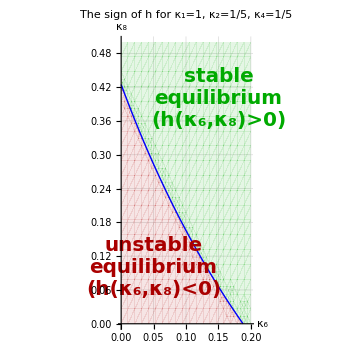

```mathematica
κ6ub=Subscript[κ, 6]/.Solve[(h/.{Subscript[κ, 8]->0})==0&&Subscript[κ, 6]>0][[1]];
κ8subst=Normal[Solve[h==0&&Subscript[κ, 6]>0&&Subscript[κ, 8]>0][[1]]];
rpl1=RegionPlot[h<0,{Subscript[κ, 6],0,1/5},{Subscript[κ, 8],0,1/2},PlotStyle->{Darker[Red],Opacity[0.1]}, BoundaryStyle->None,GridLines->Automatic,AxesLabel->{Style[Subscript[κ, 6],Bold,21,Black],Style[Subscript[κ, 8],Bold,21,Black]},Frame->None,Axes->True,PlotLabel->Style["The sign of h for κ_1=1, κ_2=1/5, κ_4=1/5",Bold,20,Black],TicksStyle->Directive[Bold, 14],ImageSize->Medium];
rpl2=RegionPlot[h>0,{Subscript[κ, 6],0,1/5},{Subscript[κ, 8],0,1/2},PlotStyle->{Darker[Green],Opacity[0.1]}, BoundaryStyle->None];
pl=Plot[Subscript[κ, 8]/.κ8subst,{Subscript[κ, 6],0,κ6ub},PlotStyle->{Blue,Thick}];
txt=Graphics[{Text[Style["unstable\nequilibrium\n(h(κ_6,κ_8)<0)",Bold,Darker[Red],20],{0.05,0.10}],
Text[Style["stable\nequilibrium\n(h(κ_6,κ_8)>0)",Bold,Darker[Green],20],{0.15,0.40}]
}];
Show[rpl1,rpl2,pl,txt]
```

#### (vi) (b) Andronov-Hopf bifurcation (compute the first focal value).

Here we compute the first focal value in the special case that is taken in part (vi) of Theorem 10. Then we plot  as a function of  (along the  curve).

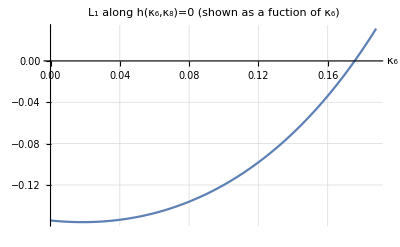

```mathematica
{A,B,CC,DD,EE}=GetDerivatives[g/.{Subscript[κ, 1]->1,Subscript[κ, 2]->1/5,Subscript[κ, 4]->1/5},equilibrium];
L1κω=GetL1[A,B,CC];
omega=Simplify[√(Det[A]/Tr[A])];
L1=Simplify[L1κω/.{ω->omega}];
L1κ6=Simplify[L1/.κ8subst];
Plot[L1κ6,{Subscript[κ, 6],0,κ6ub},GridLines->Automatic,AxesLabel->{Style[Subscript[κ, 6],Bold,21,Black],None},PlotLabel->Style["L_1 along h(κ_6,κ_8)=0\n(shown as a fuction of κ_6)",Bold,15,Black]]
```

Finally, we plot the bifurcation diagram that is also shown in the paper.

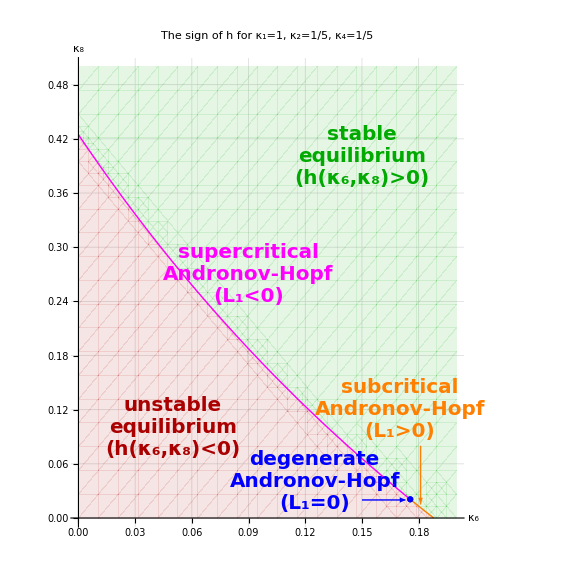

```mathematica
κ6degen=Solve[L1κ6==0&&0<Subscript[κ, 6]<κ6ub,Subscript[κ, 6]][[1]];
rpl1=RegionPlot[h<0,{Subscript[κ, 6],0,1/5},{Subscript[κ, 8],0,1/2},PlotStyle->{Darker[Red],Opacity[0.1]}, BoundaryStyle->None,GridLines->Automatic,AxesLabel->{Style[Subscript[κ, 6],Bold,21,Black],Style[Subscript[κ, 8],Bold,21,Black]},Frame->None,Axes->True,PlotLabel->Style["The sign of h for κ_1=1, κ_2=1/5, κ_4=1/5",Bold,21,Black],TicksStyle->Directive[Bold, 14],ImageSize->Large];
pl1=Plot[Subscript[κ, 8]/.κ8subst,{Subscript[κ, 6],0,Subscript[κ, 6]/.κ6degen},PlotStyle->{Magenta,Thick}];
pl2=Plot[Subscript[κ, 8]/.κ8subst,{Subscript[κ, 6],Subscript[κ, 6]/.κ6degen,κ6ub},PlotStyle->{Orange,Thick}];
lpl=ListPlot[{{Subscript[κ, 6]/.κ6degen,Subscript[κ, 8]/.κ8subst/.κ6degen}},PlotStyle->Blue,PlotMarkers->Automatic];
txt2=Graphics[{
Text[Style["supercritical\nAndronov-Hopf\n(L_1<0)",Bold,Magenta,20],{0.09,0.27}],
Text[Style["degenerate\nAndronov-Hopf\n(L_1=0)",Bold,Blue,20],{0.125,0.04}],
Text[Style["subcritical\nAndronov-Hopf\n(L_1>0)",Bold,Orange,20],{0.17,0.12}]
}];
arrow=Graphics[{{Orange,Arrow[{{0.181,0.08},{0.181,0.015}}]},{Blue,Arrow[{{0.15,0.02},{0.173,0.02}}]}}];
shw=Show[rpl1,rpl2,pl1,pl2,lpl,txt,txt2,arrow]
(*Export["C:/bboros/Dropbox/dfc1thm/3d/bimolecular_paper/F_RH_L1.jpg",shw];*)
```

#### (viii) Compute the second focal value.

```mathematica
{A,B,CC,DD,EE}=GetDerivatives[g/.{Subscript[κ, 1]->1,Subscript[κ, 2]->1/5,Subscript[κ, 4]->1/5}/.κ8subst/.N[κ6degen,20],equilibrium];
L2=GetL2[A,B,CC,DD,EE];
Print["the second focal value: ",L2];
```

the second focal value: -0.0148767997624

Thus, the second focal value is negative.

### Remark

Here we verify the claim that is made in the paper following the proof of Theorem 10. Namely, we show that whenever , along the Routh-Hurwitz curve, the first focal value is negative at , while it is positive at . W.l.o.g. we set . The calculation of  might take about four minutes.

```mathematica
{A,B,CC,DD,EE}=GetDerivatives[Simplify[g/.{Subscript[κ, 1]->1}],equilibrium];
L1κω=GetL1[A,B,CC];
triangle= 0<Subscript[κ, 2]<1&&0<Subscript[κ, 4]<1/2 (1-Subscript[κ, 2]);
```

#### Case

```mathematica
omega=Simplify[√(Det[A]/Tr[A])/.{Subscript[κ, 6]->0}];
L1=Simplify[Simplify[L1κω/.{Subscript[κ, 6]->0}]/.{ω->omega}];
RH=Simplify[A2A1minusA0/.{Subscript[κ, 1]->1,Subscript[κ, 6]->0}];
L1simp=Simplify[L1,RH==0];
Print["at  ..."];
Print["  ... Routh-Hurwitz: ",Reduce[RH==0&&triangle&&Subscript[κ, 8]>0,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 8]}]];
Print["  ...  is negative: ",Reduce[L1simp<0&&RH==0&&triangle&&Subscript[κ, 8]>0,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 8]}]];
Print["  ...  is nonnegative: ",Reduce[L1simp>=0&&RH==0&&triangle&&Subscript[κ, 8]>0,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 8]}]];
```

at  ...

... Routh-Hurwitz: 0<κ_2<1&&0<κ_4<1/2 (1-κ_2)&&κ_8==(2-6 κ_2-2 κ_2^2-9 κ_4-7 κ_2 κ_4-6 κ_4^2)/(4 (2 κ_2+3 κ_4))+1/4 √((4+8 κ_2+12 κ_2^2+8 κ_2^3+4 κ_2^4+12 κ_4+24 κ_2 κ_4+32 κ_2^2 κ_4+28 κ_2^3 κ_4+9 κ_4^2+38 κ_2 κ_4^2+73 κ_2^2 κ_4^2+12 κ_4^3+84 κ_2 κ_4^3+36 κ_4^4)/(2 κ_2+3 κ_4)^2)

...  is negative: 0<κ_2<1&&0<κ_4<1/2 (1-κ_2)&&κ_8==(2-6 κ_2-2 κ_2^2-9 κ_4-7 κ_2 κ_4-6 κ_4^2)/(4 (2 κ_2+3 κ_4))+1/4 √((4+8 κ_2+12 κ_2^2+8 κ_2^3+4 κ_2^4+12 κ_4+24 κ_2 κ_4+32 κ_2^2 κ_4+28 κ_2^3 κ_4+9 κ_4^2+38 κ_2 κ_4^2+73 κ_2^2 κ_4^2+12 κ_4^3+84 κ_2 κ_4^3+36 κ_4^4)/(2 κ_2+3 κ_4)^2)

...  is nonnegative: False

#### Case

```mathematica
omega=Simplify[√(Det[A]/Tr[A])/.{Subscript[κ, 8]->0}];
L1=Simplify[Simplify[L1κω/.{Subscript[κ, 8]->0}]/.{ω->omega}];
RH=Simplify[A2A1minusA0/.{Subscript[κ, 1]->1,Subscript[κ, 8]->0}];
L1simp=Simplify[L1,RH==0];
Print["at  ..."];
Print["  ... Routh-Hurwitz: ",Reduce[RH==0&&triangle&&Subscript[κ, 6]>0,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 6]}]];
Print["  ...  is positive: ",Reduce[L1simp>0&&RH==0&&triangle&&Subscript[κ, 6]>0,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 6]}]];
Print["  ...  is nonpositive: ",Reduce[L1simp<=0&&RH==0&&triangle&&Subscript[κ, 6]>0,{Subscript[κ, 2],Subscript[κ, 4],Subscript[κ, 6]}]];
```

at  ...

... Routh-Hurwitz: 0<κ_2<1&&0<κ_4<1/2 (1-κ_2)&&κ_6==(-3-3 κ_2-7 κ_4-κ_2 κ_4-2 κ_4^2)/(2 (2+κ_4))+1/2 √((25+10 κ_2+κ_2^2+34 κ_4+12 κ_2 κ_4+2 κ_2^2 κ_4+21 κ_4^2+10 κ_2 κ_4^2+κ_2^2 κ_4^2+12 κ_4^3+4 κ_2 κ_4^3+4 κ_4^4)/(2+κ_4)^2)

...  is positive: 0<κ_2<1&&0<κ_4<1/2 (1-κ_2)&&κ_6==(-3-3 κ_2-7 κ_4-κ_2 κ_4-2 κ_4^2)/(2 (2+κ_4))+1/2 √((25+10 κ_2+κ_2^2+34 κ_4+12 κ_2 κ_4+2 κ_2^2 κ_4+21 κ_4^2+10 κ_2 κ_4^2+κ_2^2 κ_4^2+12 κ_4^3+4 κ_2 κ_4^3+4 κ_4^4)/(2+κ_4)^2)

...  is nonpositive: False

### Remark

Consider the mass-action system (8.5) on page 109 in the book Foundations of Chemical Reaction Network Theory by Martin Feinberg.
(This is the mass-action system we call Feinberg-Berner oscillator.)
Unfortunately, with the rate constants given in the book, the unique  positive equilibrium is linearly stable, as opposed to what is claimed there.

```mathematica
κsubst={Subscript[κ, 1]->1,Subscript[κ, 2]->1,Subscript[κ, 3]->8/100,Subscript[κ, 4]->1/100,Subscript[κ, 5]->85/10,Subscript[κ, 6]->1,Subscript[κ, 7]->1,Subscript[κ, 8]->2/10};
equilibrium=Simplify[Solve[(f/.κsubst)==0&&x>0&&y>0&&z>0][[1]]];
Print["the eigenvalues: ",N[Eigenvalues[D[f/.κsubst,{{x,y,z}}]/.equilibrium]]];
```

the eigenvalues: {-11.402,-7.70911,-0.0654958}

After we have pointed this mistake out (on page 5 in https://arxiv.org/pdf/2202.11034v1.pdf ), Martin Feinberg looked into it. He found (and kindly let us know via private communication on February 27, 2022 ) that the values of  and  are accidentally swapped in the book due to a typographical error. Indeed, setting the values of  and  correctly, one finds that the equilibrium is unstable, as claimed in Section 8.3 of the book.

```mathematica
κsubst={Subscript[κ, 1]->1,Subscript[κ, 2]->1,Subscript[κ, 3]->1/100,Subscript[κ, 4]->8/100,Subscript[κ, 5]->85/10,Subscript[κ, 6]->1,Subscript[κ, 7]->1,Subscript[κ, 8]->2/10};
equilibrium=Simplify[Solve[(f/.κsubst)==0&&x>0&&y>0&&z>0][[1]]];
Print["the eigenvalues: ",N[Eigenvalues[D[f/.κsubst,{{x,y,z}}]/.equilibrium]]];
```

the eigenvalues: {-14.3295,0.0470024+0.0530062 ⅈ,0.0470024-0.0530062 ⅈ}

### Theorem 12

```mathematica
f=Subscript[κ, 1] x y{-1,-1,1,1}+Subscript[κ, 2] z w{1,1,-1,-1}+Subscript[κ, 3] z{1,0,-1,0}+Subscript[κ, 4] x{-1,0,1,0}+Subscript[κ, 5] x w{1,0,0,-1}+Subscript[κ, 6] x^2{-1,0,0,1}+Subscript[κ, 7] z{0,1,-1,0}+Subscript[κ, 8] y{0,-1,1,0};
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0&&Subscript[κ, 5]>0&&Subscript[κ, 6]>0&&Subscript[κ, 7]>0&&Subscript[κ, 8]>0;
```

#### (i) Find the curve of positive equilibria.

```mathematica
Print[Reduce[f==0&&κpositive&&x>0&&y>0&&z>0&&w>0,{x,y,z,w}]];
```

κ_1>0&&κ_2>0&&κ_3>0&&κ_4>0&&κ_5>0&&κ_6>0&&κ_7>0&&κ_8>0&&x>0&&y==(x^2 κ_2 κ_3 κ_4 κ_6+x κ_2 κ_4^2 κ_7+x κ_3 κ_4 κ_5 κ_7)/(x κ_1 κ_3^2 κ_5+κ_2 κ_3 κ_4 κ_8+κ_3^2 κ_5 κ_8)&&z==(x κ_4)/κ_3&&w==(x y κ_1-z κ_7+y κ_8)/(z κ_2)

Let us now verify that the formula given in the paper is correct.

```mathematica
equilibrium={x->t,y->(Subscript[κ, 2] Subscript[κ, 3] Subscript[κ, 6] t+Subscript[κ, 7](Subscript[κ, 2] Subscript[κ, 4]+Subscript[κ, 3] Subscript[κ, 5]))/(Subscript[κ, 1] Subscript[κ, 3] Subscript[κ, 5] t+Subscript[κ, 8](Subscript[κ, 2] Subscript[κ, 4]+Subscript[κ, 3] Subscript[κ, 5]))Subscript[κ, 4]/Subscript[κ, 3] t,z->Subscript[κ, 4]/Subscript[κ, 3] t,w->(Subscript[κ, 1] Subscript[κ, 3] Subscript[κ, 6] t+(Subscript[κ, 1] Subscript[κ, 4] Subscript[κ, 7]+Subscript[κ, 3] Subscript[κ, 6] Subscript[κ, 8]))/(Subscript[κ, 1] Subscript[κ, 3] Subscript[κ, 5] t+(Subscript[κ, 2] Subscript[κ, 4]+Subscript[κ, 3] Subscript[κ, 5]) Subscript[κ, 8])t};
Print[Simplify[f/.equilibrium]];
```

{0,0,0,0}

#### (ii) Existence and uniqueness of positive equilibria.

Suffices to check that  is strictly increasing on  for any positive , , , .

```mathematica
Print["the derivative is ",Simplify[D[(a t^2+b t)/(c t + d),t]],", which is positive"];
```

the derivative is (b d+a t (2 d+c t))/(d+c t)^2, which is positive

#### (iii) Toricity is equivalent to complex balancing.

```mathematica
Print[Reduce[(Subscript[κ, 2] Subscript[κ, 6])/(Subscript[κ, 1] Subscript[κ, 5])==Subscript[κ, 7]/Subscript[κ, 8]&&κpositive]];
Print[Reduce[Subscript[κ, 6]/Subscript[κ, 5]==(Subscript[κ, 1] Subscript[κ, 4] Subscript[κ, 7]+Subscript[κ, 3] Subscript[κ, 6] Subscript[κ, 8])/((Subscript[κ, 2] Subscript[κ, 4]+Subscript[κ, 3] Subscript[κ, 5]) Subscript[κ, 8])&&κpositive]];
```

κ_3>0&&κ_4>0&&κ_2>0&&κ_5>0&&κ_6>0&&κ_7>0&&κ_8>0&&κ_1==(κ_2 κ_6 κ_8)/(κ_5 κ_7)

κ_2>0&&κ_3>0&&κ_4>0&&κ_5>0&&κ_6>0&&κ_7>0&&κ_8>0&&κ_1==(κ_2 κ_6 κ_8)/(κ_5 κ_7)

#### (v) The Jacobian matrix and its determinant.

```mathematica
J=Simplify[D[f[[1;;3]]/.{w->c-x-y-z},{{x,y,z}}]/.{x->0,y->0,z->0}];
Print["the Jacobian matrix of the reduced system: ",MatrixForm[J]];
Print["its determinant: ",Simplify[Det[J]]];
```

the Jacobian matrix of the reduced system: (-κ_4+c κ_5 | 0 | c κ_2+κ_3
0 | -κ_8 | c κ_2+κ_7
κ_4 | κ_8 | -c κ_2-κ_3-κ_7)

its determinant: c (κ_2 κ_4+κ_3 κ_5) κ_8

## 4 Wilhelm-Heinrich oscillator

### Theorem 13

```mathematica
f= Subscript[κ, 1] x  {1,0,0}+Subscript[κ, 2] x y {-1,0,0}+Subscript[κ, 3] y {0,-1,0}+Subscript[κ, 4] x {-1,0,1}+Subscript[κ, 5] z {0,1,-1};
```

#### (i) The unique positive equilibrium.

```mathematica
Print[Reduce[f==0&&Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0&&Subscript[κ, 5]>0&&x>0&&y>0&&z>0,{y,x,z}]];
```

κ_1>0&&0<κ_4<κ_1&&κ_2>0&&κ_3>0&&κ_5>0&&y==-(-κ_1+κ_4)/κ_2&&x==(y κ_3)/κ_4&&z==(y κ_3)/κ_5

```mathematica
equilibrium={x->(Subscript[κ, 1]-Subscript[κ, 4])/Subscript[κ, 2] Subscript[κ, 3]/Subscript[κ, 4],y->(Subscript[κ, 1]-Subscript[κ, 4])/Subscript[κ, 2],z->(Subscript[κ, 1]-Subscript[κ, 4])/Subscript[κ, 2] Subscript[κ, 3]/Subscript[κ, 5]};
```

#### (ii) The system is competitive.

After performing the  coordinate transformation, all the off-diagonal entries are nonpositive everywhere on.

```mathematica
Print[MatrixForm[D[(f/.{z->-w}){1,1,-1},{{x,y,w}}]]];
```

(κ_1-y κ_2-κ_4 | -x κ_2 | 0
0 | -κ_3 | -κ_5
-κ_4 | 0 | -κ_5)

#### (iv) The Routh-Hurwitz criterion and the first focal value.

```mathematica
{A,B,CC,DD,EE}=GetDerivatives[f,equilibrium];
{charpol,Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],A2A1minusA0}=GetHopf[A];
Print["Jacobian matrix: ",MatrixForm[Simplify[A]]];
Print["characteristic polynomial: ",charpol];
Print["with  being the coefficient of , the expression  equals ",Collect[A2A1minusA0,t]];
Hopf=FullSimplify[Normal[Solve[A2A1minusA0==0&&Subscript[κ, 3]>0][[1]]]];
Print["Routh-Hurwitz: ",Hopf];
```

Jacobian matrix: (0 | κ_3 (1-κ_1/κ_4) | 0
0 | -κ_3 | κ_5
κ_4 | 0 | -κ_5)

characteristic polynomial: λ^3+λ κ_3 κ_5+κ_1 κ_3 κ_5-κ_3 κ_4 κ_5+λ^2 (κ_3+κ_5)

with  being the coefficient of , the expression  equals κ_3 κ_5 (-κ_1+κ_3+κ_4+κ_5)

Routh-Hurwitz: {κ_1→κ_3+κ_4+κ_5}

Next, we verify that the first focal value is indeed negative.

```mathematica
L1pqrsω=GetL1[A,B,CC];
omega=Simplify[√(Det[A]/Tr[A])];
L1=Factor[L1pqrsω/.{ω->omega}/.Hopf];
Print["the first focal value: ",L1];
```

the first focal value: -(κ_2^2 κ_5^3)/((κ_3^2+3 κ_3 κ_5+κ_5^2) (κ_3^2+6 κ_3 κ_5+κ_5^2))

### Theorem 14

```mathematica
f= x w {1,0,0,-1}+p x y {-1,0,0,1}+q y {0,-1,0,1}+r x {-1,0,1,0}+s z {0,1,-1,0};
```

#### (i) Line of equilibria.

```mathematica
Print[Simplify[Reduce[f==0&&p>0&&q>0&&r>0&&s>0&&x>0&&y>0&&z>0&&w>0,{x,y,z,w}]]];
```

s>0&&r>0&&q>0&&p>0&&x>0&&y==(r x)/q&&(q y)/s==z&&r+p y==w

```mathematica
equilibrium={x->t,y->t r/q,z->t r/s,w->(t p/q+1)r};
Print[Simplify[f/.equilibrium]];
```

{0,0,0,0}

#### (ii) The Routh-Hurwitz criterion.

```mathematica
c=(x+y+z+w/.equilibrium);
f2=f[[1;;3]]/.{w->c-x-y-z};
Clear[c];
{A,B,CC,DD,EE}=GetDerivatives[f2,equilibrium];
{charpol,Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],A2A1minusA0}=GetHopf[A];
Print["Jacobian matrix: ",MatrixForm[Simplify[A]]];
Print["characteristic polynomial: ",charpol];
Print["with  being the coefficient of , the expression  equals ",Collect[A2A1minusA0,t]];
Hopf=FullSimplify[Normal[Solve[A2A1minusA0==0][[1]]]];
Print["Routh-Hurwitz: ",Hopf];
```

Jacobian matrix: (-t | -((1+p) t) | -t
0 | -q | s
r | 0 | -s)

characteristic polynomial: q r t+q s t+r s t+p r s t+(q s+q t+r t+s t) λ+(q+s+t) λ^2+λ^3

with  being the coefficient of , the expression  equals q^2 s+q s^2+(q^2+2 q s-p r s+s^2) t+(q+r+s) t^2

Routh-Hurwitz: {p→(q s (q+s)+(q+s)^2 t+(q+r+s) t^2)/(r s t)}

#### (iii) The first focal value.

```mathematica
L1pqrsω=GetL1[A,B,CC];
omega=Simplify[√(Det[A]/Tr[A])];
L1=Simplify[L1pqrsω/.{ω->omega}/.Hopf];
Print["the first focal value: ",L1];
```

the first focal value: -((q+t) (s+t) (s^2+r t+s t+q (s+t)) ((r+s) (s-t) t+q^2 (2 s+t)+q (2 s^2+2 s t+(r-t) t)))/(2 r^2 t^2 (q^4+s^4+9 s^3 t+9 s t^2 (2 r+t)+9 q^3 (s+t)+5 s^2 t (r+4 t)+t^2 (4 r^2+5 r t+t^2)+9 q (s+t) (s^2+4 s t+t (2 r+t))+5 q^2 (4 s^2+9 s t+t (r+4 t))))

We omit the factors with purely positive terms.

```mathematica
L1qrst=-((r+s) (s-t) t+q^2 (2 s+t)+q (2 s^2+2 s t+(r-t) t));
Print[Simplify[CoefficientList[L1qrst,t]]];
```

{-2 q s (q+s),-((q+s) (q+r+s)),q+r+s}

We now find values of , , ,  for which there are two Hopf points, and the sign of the first focal value at those points have opposite sign.

```mathematica
pqrssubst={p->8,q->1,r->2,s->1};
roots=Solve[(A2A1minusA0/.{p->8,q->1,r->2,s->1})==0];
Print["the two roots: ",roots];
Print[" at the 1st root: ",Simplify[L1qrst/.pqrssubst/.roots[[1]]]];
Print[" at the 2nd root: ",Simplify[L1qrst/.pqrssubst/.roots[[2]]]];
```

the two roots: {{t→1/2 (3-√7)},{t→1/2 (3+√7)}}

at the 1st root: -2 √7

at the 2nd root: 2 √7

Next, we show an instance, where the first focal value vanishes. We analyse this situation further in (vi) below.

```mathematica
pqrstsubst={p->3(1+√2),q->1,r->2,s->1,t->1+√2};
Print[" = ",Simplify[A2A1minusA0/.pqrstsubst]];
Print[" = ",Simplify[L1qrst/.pqrstsubst]];
```

= 0

= 0

#### (v) The first focal value is negative at the lower Hopf point.

Here we check using computer algebra that the first focal value at the lower Hopf point never nonnegative, i.e., it is always negative. For a formal proof, see the paper.

```mathematica
coeffs=Simplify[CoefficientList[A2A1minusA0,t]];
Print[Reduce[A2A1minusA0==0&&L1qrst>=0&&p>0&&q>0&&r>0&&s>0&&t>0&&t<-coeffs[[2]]/(2coeffs[[3]])]];
```

False

#### (vi) The second focal value.

The computation below might take a little longer, approximately 1-2 minutes. This is because a number of times FullSimplify is employed for involved nonreal expressions with square roots.

```mathematica
pqrstsubst={p->3(1+√2),q->1,r->2,s->1,t->1+√2};
{A,B,CC,DD,EE}=GetDerivatives[f2/.pqrstsubst,equilibrium/.pqrstsubst];
A=Simplify[A];
omega=Simplify[√(Det[A]/Tr[A])];
L2=GetL2[A,B,CC,DD,EE];
Print["the second focal value: ",L2,"  ",N[L2]];
```

the second focal value: -55/4116+5/(343 √2)  -0.00305481

Finally, we plot the bifurcation diagram that is also shown in the paper.

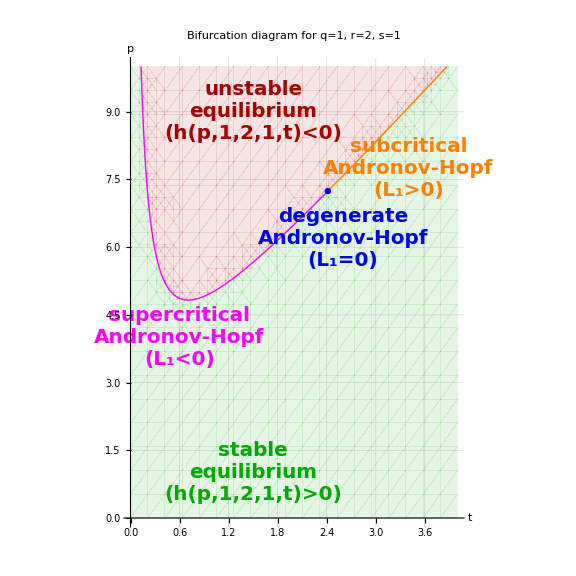

```mathematica
qrssubst={q->1,r->2,s->1};
rpl1=RegionPlot[(A2A1minusA0/.qrssubst)<0,{t,0,4},{p,0,10},PlotStyle->{Darker[Red],Opacity[0.1]}, BoundaryStyle->None,GridLines->Automatic,AxesLabel->{Style[t,Bold,21,Black],Style[p,Bold,21,Black]},Frame->None,Axes->True,PlotLabel->Style["Bifurcation diagram for q=1, r=2, s=1",Bold,21,Black],TicksStyle->Directive[Bold, 14],ImageSize->Large];
rpl2=RegionPlot[(A2A1minusA0/.qrssubst)>0,{t,0,4},{p,0,10},PlotStyle->{Darker[Green],Opacity[0.1]}, BoundaryStyle->None];
pl1=Plot[p/.Hopf/.qrssubst,{t,0,1+√2},PlotStyle->{Magenta,Thick},PlotRange->{{0,10}}];
pl2=Plot[p/.Hopf/.qrssubst,{t,1+√2,4},PlotStyle->{Orange,Thick},PlotRange->{{0,10}}];
lpl=ListPlot[{{1+√2,3 (1+√2)}},PlotStyle->Blue,PlotMarkers->Automatic];
txt=Graphics[{
Text[Style["unstable\nequilibrium\n(h(p,1,2,1,t)<0)",Bold,Darker[Red],20],{1.5,9}],
Text[Style["stable\nequilibrium\n(h(p,1,2,1,t)>0)",Bold,Darker[Green],20],{1.5,1}],
Text[Style["supercritical\nAndronov-Hopf\n(L_1<0)",Bold,Magenta,20],{0.6,4}],
Text[Style["degenerate\nAndronov-Hopf\n(L_1=0)",Bold,Blue,20],{2.6,6.2}],
Text[Style["subcritical\nAndronov-Hopf\n(L_1>0)",Bold,Orange,20],{3.4,7.75}]
}];
shw=Show[rpl1,rpl2,pl1,pl2,lpl,txt]
(*Export["C:/bboros/Dropbox/dfc1thm/3d/bimolecular_paper/WH_RH_L1.jpg",shw];*)
```

#### (vii) The eigenvalues at the corner equilibrium .

```mathematica
Clear[c];
J=Simplify[D[f[[1;;3]]/.{w->c-x-y-z},{{x,y,z}}]];
Print["the eigenvalues of the reduced system at the corner equilibrium : ",Eigenvalues[J/.{x->0,y->0,z->0}]];
```

the eigenvalues of the reduced system at the corner equilibrium : {-q,c-r,-s}

## 5 Wilhelm oscillator

### Theorem 15

```mathematica
f=Subscript[κ, 1] y{0,1,0}+Subscript[κ, 2] x^2{-2,0,1}+Subscript[κ, 3] y z{1,-1,0}+Subscript[κ, 4] z^2{0,0,-2};
```

#### (i) The system is competitive.

After performing the  coordinate transformation, all the off-diagonal entries are nonpositive everywhere on.

```mathematica
Print[MatrixForm[D[(f/.{x->-w}){-1,1,1},{{w,y,z}}]]];
```

(4 w κ_2 | -z κ_3 | -y κ_3
0 | κ_1-z κ_3 | -y κ_3
2 w κ_2 | 0 | -4 z κ_4)

#### (ii) The unique positive equilibrium.

```mathematica
equilibrium=Simplify[Normal[Solve[f==0&&Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0&&x>0&&y>0&&z>0,{x,y,z}][[1]]],Subscript[κ, 1]>0&&Subscript[κ, 3]>0];
Print["equilibrium: ",equilibrium];
```

equilibrium: {x→(√2 κ_1 √(κ_4/κ_2))/κ_3,y→(4 κ_1 κ_4)/κ_3^2,z→κ_1/κ_3}

#### (iii) The first focal value.

```mathematica
reparam={Subscript[κ, 1]->Subscript[κ, 2] p/r,Subscript[κ, 3]->Subscript[κ, 2] p,Subscript[κ, 4]->Subscript[κ, 2] q^2/2};
f2=Expand[Simplify[Subscript[κ, 3]/(Subscript[κ, 1] Subscript[κ, 2])f/.reparam]];
Print["reparametrised ODE: ",MatrixForm[{,,}],"=",MatrixForm[f2]];
equilibrium2=Simplify[equilibrium/.reparam,q>0];
Print["equilibrium: ",equilibrium2];
{A,B,CC,DD,EE}=GetDerivatives[f2,equilibrium2];
{charpol,Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],A2A1minusA0}=GetHopf[A];
Print["Jacobian matrix: ",MatrixForm[A]];
Print["characteristic polynomial: ",charpol];
linstable=Reduce[Expand[A2A1minusA0]>0&&p>0&&q>0&&r>0];
Print["all eigenvalues have negative real part: ",linstable];
Hopf=Simplify[Normal[Solve[A2A1minusA0==0&&q>0][[1]]]];
L1pqrω=GetL1[A,B,CC];
omega=Simplify[√(Det[A]/Tr[A])];
L1=Factor[Simplify[L1pqrω/.{ω->omega}/.Hopf]];
Print["the first focal value: ",L1];
```

reparametrised ODE: (ẋ
ẏ
ż)=(-2 r x^2+p r y z
p y-p r y z
r x^2-q^2 r z^2)

equilibrium: {x→q/r,y→(2 q^2)/(p r),z→1/r}

Jacobian matrix: (-4 q | p | 2 q^2
0 | 0 | -2 q^2
2 q | 0 | -2 q^2)

characteristic polynomial: 4 p q^3+4 q^3 λ+(4 q+2 q^2) λ^2+λ^3

all eigenvalues have negative real part: q>0&&0<p<4 q+2 q^2&&r>0

the first focal value: -(q (4+12 q+17 q^2+11 q^3+3 q^4) r^2)/((1+q) (4+q) (4+8 q+q^2))

### Theorem 16

```mathematica
f=Subscript[κ, 1] y w{0,1,0,-1}+Subscript[κ, 2] x^2{-2,0,1,1}+Subscript[κ, 3] y z{1,-1,0,0}+Subscript[κ, 4] z^2{0,0,-2,2};
```

#### (ii) The line of positive equilibria.

```mathematica
Print[Simplify[Normal[Solve[f==0&&Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0&&x>0&&y>0&&z>0&&w>0,{x,y,w}][[1]]],z>0]];
```

{x→√2 z √(κ_4/κ_2),y→(4 z κ_4)/κ_3,w→(z κ_3)/κ_1}

```mathematica
equilibrium={x->√((2 Subscript[κ, 4])/Subscript[κ, 2])t,y->(4 Subscript[κ, 4])/Subscript[κ, 3] t,z->t,w->Subscript[κ, 3]/Subscript[κ, 1] t};
```

#### (iii) The Routh-Hurwitz criterion.

We start by reparametrising the ODE.

```mathematica
f2=Expand[Simplify[Subscript[κ, 3]/(Subscript[κ, 1] Subscript[κ, 2])f/.reparam]];
Print["reparametrised ODE: ",MatrixForm[{,,,}],"=",MatrixForm[f2]];
equilibrium2=Simplify[equilibrium/.reparam,q>0];
Print["equilibrium: ",equilibrium2];
equilibrium2=equilibrium2/.{t->1};
c=(x+y+z+w/.equilibrium2);
f3=f2[[1;;3]]/.{w->c-x-y-z};
Clear[c];
{A,B,CC,DD,EE}=GetDerivatives[f3,equilibrium2];
{charpol,Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],A2A1minusA0}=GetHopf[A];
Print["Jacobian matrix: ",MatrixForm[A]];
Print["characteristic polynomial: ",charpol];
linstable=Reduce[Expand[A2A1minusA0]>0&&p>0&&q>0&&r>0];
Print["all eigenvalues have negative real part: ",linstable];
Hopf=FullSimplify[Normal[Solve[A2A1minusA0==0&&q>0][[1]]]];
Print["Routh-Hurwitz: ",Hopf];
```

reparametrised ODE: (ẋ
ẏ
ż
ẇ)=(-2 r x^2+p r y z
p w y-p r y z
r x^2-q^2 r z^2
r x^2-p w y+q^2 r z^2)

equilibrium: {x→q t,y→(2 q^2 t)/p,z→t,w→r t}

Jacobian matrix: (-4 q r | p r | 2 q^2 r
-2 q^2 | -2 q^2 | -2 q^2-2 q^2 r
2 q r | 0 | -2 q^2 r)

characteristic polynomial: 4 p q^3 r^2+4 p q^4 r^2+8 q^5 r^2+4 p q^3 r^3+(2 p q^2 r+8 q^3 r+4 q^4 r+4 q^3 r^2) λ+(2 q^2+4 q r+2 q^2 r) λ^2+λ^3

all eigenvalues have negative real part: (0<r≤1&&q>0&&p>0)||(r>1&&((0<q<-r+r^2&&0<p<(-4 q^2-2 q^3-8 q r-8 q^2 r-2 q^3 r-4 q r^2-2 q^2 r^2)/(q+r-r^2))||(q≥-r+r^2&&p>0)))

Routh-Hurwitz: {p→-(2 q (2+q) (q+(2+q) r+r^2))/(q+r-r^2)}

#### (iv) The first focal value.

This might take 1-2 minutes.

```mathematica
L1pqrω=GetL1[A,B,CC];
omega=Simplify[√(Det[A]/Tr[A])];
L1=Simplify[L1pqrω/.{ω->omega}/.Hopf];
Print["the first focal value: ",L1];
Print[" negative: ",Reduce[L1<0&&r>1&&0<q<r(r-1)]];
Print[" vanishes: ",Reduce[L1==0&&r>1&&0<q<r(r-1)]];
Print[" positive: ",Reduce[L1>0&&r>1&&0<q<r(r-1)]];
```

the first focal value: ((q r (2+q^2+3 r+r^2+2 q (1+r)) (8 r^5 (2-3 r+r^3)+8 q r^5 (-4-13 r+14 r^2+3 r^3)+2 q^7 r (2-5 r+r^2+r^3+r^4)+2 q^6 r (10-15 r-26 r^2+18 r^3+13 r^4+4 r^5)+2 q^2 r^3 (14+19 r-62 r^2+176 r^3+160 r^4+17 r^5)+2 q^3 r^2 (6+41 r-98 r^2+136 r^3+371 r^4+137 r^5+11 r^6)+q^4 r (-2+51 r-154 r^2-213 r^3+493 r^4+414 r^5+101 r^6+6 r^7)+q^5 (-2+25 r+5 r^2-210 r^3+15 r^4+209 r^5+86 r^6+16 r^7)))/(2 (q+r-r^2) (16 (-1+r)^2 r^6+q^6 (1+4 r+r^2-6 r^3)+4 q r^5 (6-21 r+2 r^2+13 r^3)+4 q^2 r^4 (10-28 r-15 r^2+31 r^3+12 r^4)+q^5 r (10+20 r-27 r^2-35 r^3+5 r^4+3 r^5)+q^3 r^3 (38-85 r-174 r^2+60 r^3+84 r^4+13 r^5)+q^4 r^2 (31-3 r-130 r^2-45 r^3+42 r^4+12 r^5+r^6))))

negative: r>1&&0<q<-r+r^2

vanishes: False

positive: False

#### (vi) The eigenvalues at the corner equilibria and .

```mathematica
J=Simplify[D[f[[1;;3]]/.{w->c-x-y-z},{{x,y,z}}]];
Print["the eigenvalues of the reduced system at the corner equilibrium ..."];
Print["  ... : ",Eigenvalues[J/.{x->0,y->0,z->0}]];
Print["  ... : ",Eigenvalues[J/.{x->0,y->c,z->0}]];
```

the eigenvalues of the reduced system at the corner equilibrium ...

... : {c κ_1,0,0}

... : {0,0,-c κ_1}